```mathematica
Needs["PlotLegends`"]
```

```mathematica
hetFunc[t_, H0_, Ne_]:=H0*(1-1/(2*Ne))^t;
```

```mathematica
myH0=0.34;
Ne=2*100;
```

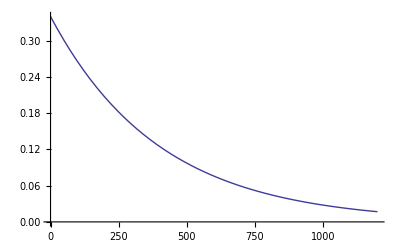

```mathematica
Plot[hetFunc[t, myH0,Ne],{t,0,6*Ne},PlotRange->{{0,6*Ne},{0,myH0}}]
```

```mathematica
FstFunc[t_,H0_,Ne_]:=Module[{H1},
H1=0.5;
Return[(H1-hetFunc[t,H0,Ne])/H1]
]
```

```mathematica
Ne1=2*10^2;
Ne2=2*10^3;
Ne3=2*10^4;
Ne4=2*10^5;
Ne5=2*10^6;
Ne6=2*10^7;
```

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

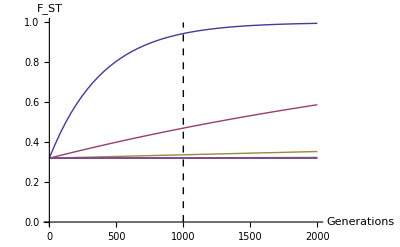

```mathematica
Show[Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,10*Ne},PlotRange->{{0,10*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"}],Graphics[{Dashed,Thin,Line[{{1000,0},{1000,1.}}]}]]
```

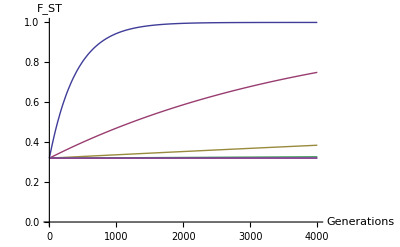

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,20*Ne},PlotRange->{{0,20*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

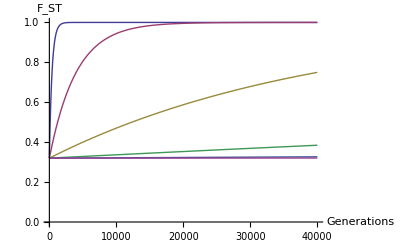

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,200*Ne},PlotRange->{{0,200*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

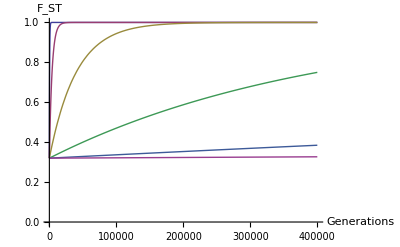

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,2000*Ne},PlotRange->{{0,2000*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

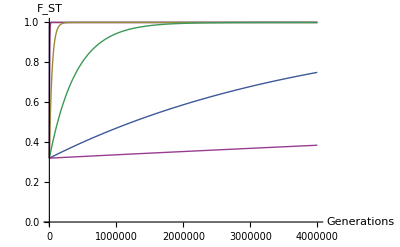

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,20000*Ne},PlotRange->{{0,20000*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

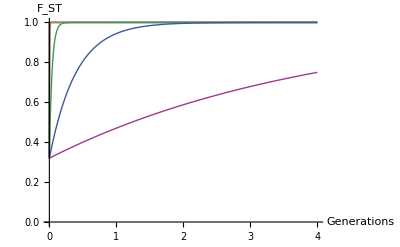

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,200000*Ne},PlotRange->{{0,200000*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,200000*Ne},PlotRange->{{0,200000*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

-Graphics-

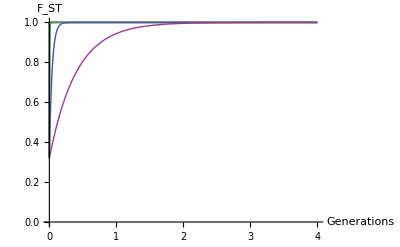

```mathematica
Plot[{FstFunc[t,myH0,Ne1],FstFunc[t,myH0,Ne2],FstFunc[t,myH0,Ne3],FstFunc[t,myH0,Ne4],FstFunc[t,myH0,Ne5],FstFunc[t,myH0,Ne6]},{t,0,2000000*Ne},PlotRange->{{0,2000000*Ne},{0.,1.}},AxesLabel->{"Generations","F_ST"} ,PlotLegend->{"N_e = 2*10^2","N_e = 2*10^3","N_e = 2*10^4","N_e = 2*10^5","N_e = 2*10^6","N_e = 2*10^7"},LegendPosition->{1.2,-0.5},LegendShadow->None,LegendSize->{0.75,0.9}]
```

```mathematica
NeVec={2*10^2,2*10^3,2*10^4,2*10^5,2*10^6,2*10^7};
```

```mathematica
mVec=2/NeVec;
```

```mathematica
NeVec*mVec
```

{2,2,2,2,2,2}

The predicted equilibrium value of F_STunder drift and migration, with d demes, was derived by several authors (Takahata 1983, Crow and Aoki 1984, Slatkin 1995) as

F_ST=1/(1+(4m d^2 N_e)/(d-1)^2)≈1/(1+4 N_e m),

```mathematica
FST[M_,d_]:=1/(1+(4 M d^2 )/((d-1)^2))
```

where N_e is the effective size of a local deme and m is the migration rate. Furthermore, the approximation applies for large d. Applying this to the case of d=2 and M=N_e m = 2, we obtain

```mathematica
FST[2,2]
```

1/33

This is the F_STvalue I would expect to see for large K if the experiments were run for long enough (about 8*K generations). After that time, one can expect that the drift-migration equilibrium has been reached.

The equilibrium values for other numbers of migrants are as follows:

M=1

```mathematica
FST[1,2]
```

1/17

M=5

```mathematica
FST[5,2]
```

1/81

M=50

```mathematica
FST[50,2]
```

1/801

Equilibrium values of F_ST for varying migrant numbers M and d=2 demes.

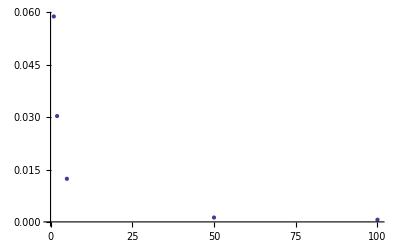

```mathematica
ListPlot[Table[{i,FST[i,2]},{i,{1,2,5,50,100}}]]
```